# Butterfly Mimicry

Kui.Chen 2016/02/15 Monday

## Implementation

### Options

These options are used to set the attributes and output format in Butterfly Camouflage Evolution.

```mathematica
(*These 3 options are used to control the output format*)
Options[displayWorldSpot]={
BackgroundHue->0.9,ColoringFunction->GrayLevel
};
Options[butterflyGraphics]={
BackgroundHue->0.9,ColoringFunction->GrayLevel
};
Options[displayButterflyWorld]={DisplayMatrixWidth->0};

(*These options are used to control the properties in the evolution*)
Options[mutation]={
MutationProbability->0.0,MutationRange->0.1
};
Options[reduction]:={BackgroundHue->0.5};
Options[evolveButterflies]={
InitialPopulation->{},
WorldWidth->10,
ButterflyProbability->0.5,
ReductionCreationPortion->0.1,
BackgroundHue->0.5,
ColoringFunction->Hue,
DisplayMatrixWidth->0,
Generations->10,
MutationProbability->.2,
MutationRange->0.1
};
```

### Generating an Initial Butterfly Vector

Generating butterfly or tree trunk according to the random real number.{1, _} represents the butterfly, while the {0, BGColor} represents the tree trunk.

```mathematica
createWorld[width_:100,butProb_:0.5,opts___]:=Table[
If[RandomReal[]<butProb,
{1,RandomReal[]},
{0,BGColor}
],
width
];
```

#### Test

Test createWorld function.

```mathematica
butterflies=createWorld[10,0.5]
```

{{0,BGColor},{0,BGColor},{0,BGColor},{1,0.0591787},{0,BGColor},{1,0.164654},{1,0.0946192},{0,BGColor},{1,0.299958},{1,0.0221191}}

```mathematica
butterflies//TableForm
```

0 | BGColor
0 | BGColor
0 | BGColor
1 | 0.0591787
0 | BGColor
1 | 0.164654
1 | 0.0946192
0 | BGColor
1 | 0.299958
1 | 0.0221191

### Visualization

#### Display one butterfly on the tree trunk.

```mathematica
displayWorldSpot[{0,color_},opts___]:=Graphics[
Hue[0],
Background->(ColoringFunction/.{opts}/.Options[displayWorldSpot])[BackgroundHue/.{opts}/.Options[displayWorldSpot]]
];
displayWorldSpot[{1,color_},opts___]:=butterflyGraphics[color,opts];
```

#### Draw one butterfly.

```mathematica
butterflyGraphics[color_,opts___]:=Block[
{p,q,colFunc},
colFunc=ColoringFunction/.{opts}/.Options[butterflyGraphics];
Graphics[
{
colFunc[color],
Polygon[p={{0,0},{1,3},{5,0},{5,12},{1,8},{0,9}}],
Polygon[q=({-1,1} #1&)/@p],
GrayLevel[0.0],
Line[p],
Line[q],
Line[{{0,9},{-2,12}}],
Line[{{0,9},{2,12}}]
},
Background->colFunc[BackgroundHue/.{opts}/.Options[butterflyGraphics]],
PlotRange->{{-6,6},{-1,13}}
]
];
```

#### Generate all butterflies

```mathematica
displayButterflyWorld[buts_List,opts___]:=Block[
{dispMatrixWidth},
dispMatrixWidth=DisplayMatrixWidth/.{opts}/.Options[displayButterflyWorld];
If[dispMatrixWidth===0,dispMatrixWidth=Length[buts]];
Show[
GraphicsGrid[
Partition[(displayWorldSpot[#1,opts]&)/@buts,dispMatrixWidth]
]
]
];
```

#### Test

Test displayWorldSpot function.

```mathematica
displayWorldSpot[{0,.8},BackgroundHue->0.4]
```

-Graphics-

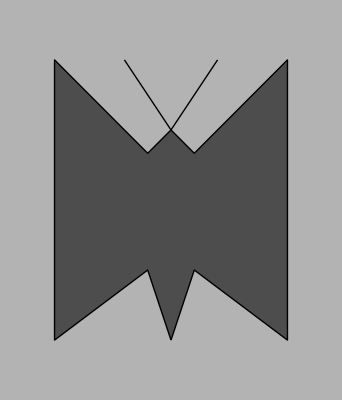

```mathematica
displayWorldSpot[{1,0.3},BackgroundHue->0.7]
```

Test butterflyGraphics function.

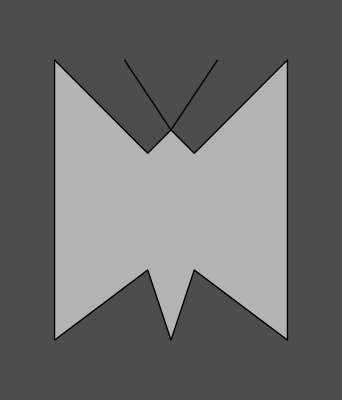

```mathematica
butterflyGraphics[0.7,BackgroundHue->0.3]
```

Test displayButterflyWorld function.

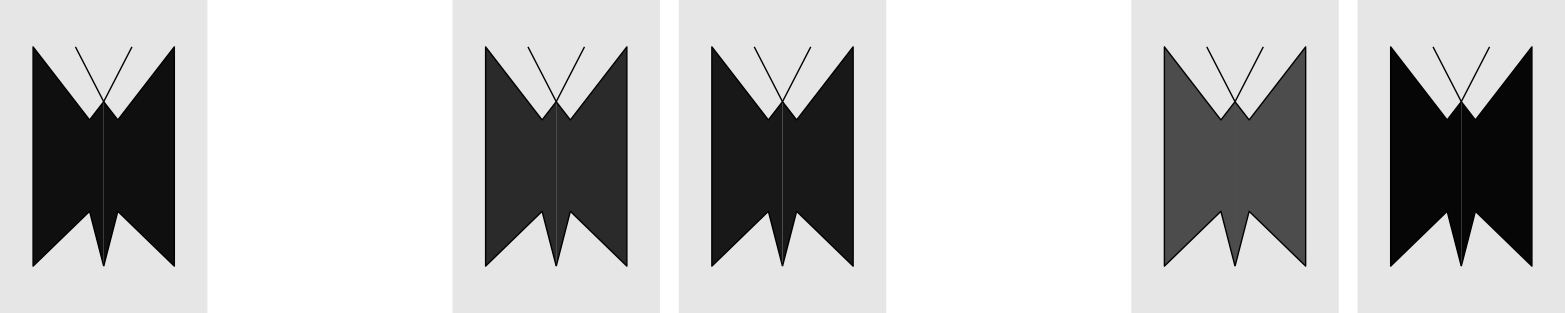

```mathematica
displayButterflyWorld[butterflies]
```

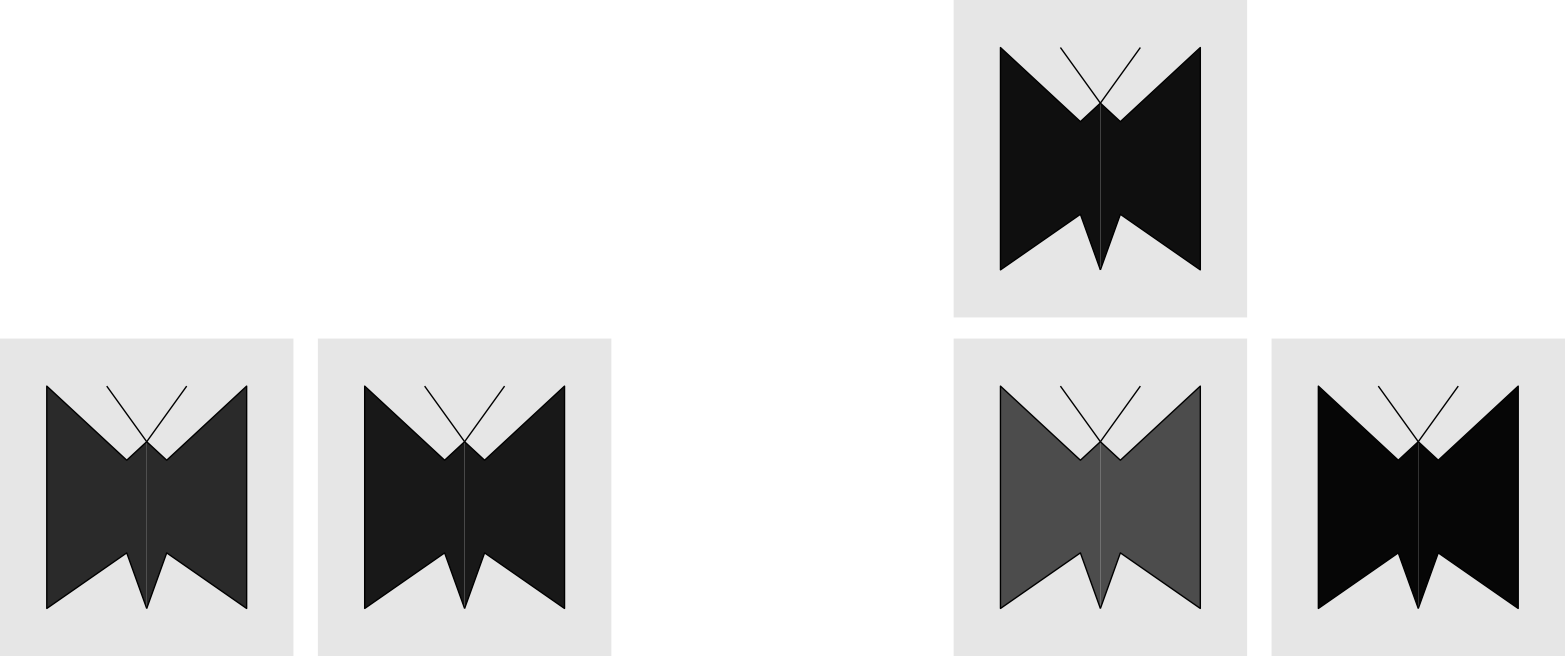

```mathematica
displayButterflyWorld[butterflies,DisplayMatrixWidth->5]
```

### Fitness and Misfitness

The fitness of a butterfly is calculated as:
            fitness = 1/(butterfly_color-background_color)
and the misfitness is:
            misfitness = butterfly_color - background_color.
The larger the misfitness, the higher probability the butterfly will be removed from the tree trunk (ie. eaten by a bird).

```mathematica
butterflyMisfitness[color_,bgColor_]:=Abs[color-bgColor]
butterflyMisfitness[BGColor,_]:=0
```

#### Test

Test butterflyMisfitness function.

```mathematica
misfits=butterflyMisfitness[Last[#],0.9]&/@Cases[butterflies,{1,_}]
```

{0.840821,0.735346,0.805381,0.600042,0.877881}

```mathematica
fits=(#/(Plus@@fits)&)/@misfits
```

{0.217859,0.19053,0.208676,0.155473,0.227461}

```mathematica
Total[fits]
```

1.

### Mutation

We mutate the butterfly’s color by adding a random real Δcolor

```mathematica
mutation[{1,c_},opts___]:=Block[
{mutRange},

mutRange=MutationRange/.{opts}/.Options[mutation];
If[RandomReal[]<(MutationProbability/.{opts}/.Options[mutation]),
{1,Mod[c+RandomReal[{-mutRange,mutRange}],1.0]},
{1,c}
]
];
mutation[{0,c_},___]:={0,c};
```

#### Test

Test mutation function.

```mathematica
mutatedButterflies=mutation[#,MutationProbability->0.4,MutationRange->0.2]&/@butterflies
```

{{0,BGColor},{0,BGColor},{0,BGColor},{1,0.240632},{0,BGColor},{1,0.164654},{1,0.0946192},{0,BGColor},{1,0.15989},{1,0.0221191}}

```mathematica
mutatedButterflies//TableForm
```

0 | BGColor
0 | BGColor
0 | BGColor
1 | 0.240632
0 | BGColor
1 | 0.164654
1 | 0.0946192
0 | BGColor
1 | 0.15989
1 | 0.0221191

Now, you can compare it with butterflies.

```mathematica
butterflies//TableForm
```

0 | BGColor
0 | BGColor
0 | BGColor
1 | 0.0591787
0 | BGColor
1 | 0.164654
1 | 0.0946192
0 | BGColor
1 | 0.299958
1 | 0.0221191

### Selection and Evolution

#### Reduction

Reduction function is used to remove a butterfly from tree trunk. Firstly, we calculate the misfitnesses of all butterflies. Then, randomly select a butterfly. Keep in mind that the higher the misfitness is, the higher probability that the butterfly will be selected and removed is.

```mathematica
reduction[pop_List,opts___]:=Block[
{r,fitnesses},

bgHue=BackgroundHue/.{opts}/.Options[reduction];
fitnesses=(butterflyMisfitness[#1,bgHue]&)/@((#1⟦2⟧&)/@pop);
ReplacePart[pop,fitnessProportionalSelection[fitnesses]->{0,BGColor}]
];
```

#### Create new butterfly

Once a butterfly is removed, a new butterfly have to be added to the tree trunk. Here, we just randomly select one from the survived butterflies, mutate it and put it on a random place of the tree trunk.

```mathematica
creation[pop_List,opts___]:=Block[
{butPositions,selectedButIndex,nonButPositions,selectedNonButIndex},

butPositions=Flatten[Position[pop,{1,_}]];
selectedButIndex=randomSelection[butPositions];

nonButPositions=Flatten[Position[pop,{0,_}]];
selectedNonButIndex=randomSelection[nonButPositions];

ReplacePart[pop,selectedNonButIndex->mutation[pop⟦selectedButIndex⟧,opts]]
];
```

#### Fitness Proportional Selection

Select a butterfly according to the misfitness.

```mathematica
fitnessProportionalSelection[fits_List]:=Block[
{randpos,members=Length[fits],totalsum=Total[fits],partsum=First[fits],index=1},

randpos=RandomReal[{0,N[totalsum]}];
(*NestWhile[#+=fits⟦index⟧&,partsum,partsum<randpos&&index++];
Return[index]*)
While[partsum<randpos&&index<members,index=index+1;partsum=partsum+fits⟦index⟧;
];
index
];
```

#### Auxiliary Functions

```mathematica
randomSelection[elements_List]:=elements⟦RandomInteger[{1,Length[elements]}]⟧
```

```mathematica
creationIterated[pop_List,iter_Integer:1,opts___]:=
Nest[creation[#1,opts]&,pop,iter];
```

```mathematica
reductionIterated[pop_List,iter_Integer:1,opts___]:=Nest[reduction[#1,opts]&,pop,iter];
```

```mathematica
reductionAndCreation[pop_List,indivs_Integer:1,opts___]:=creationIterated[reductionIterated[pop,indivs,opts],indivs,opts];
```

#### Test

Test fitnessProportionalSelection function.

```mathematica
fitnessProportionalSelection[misfits]
```

4

Test reduction function.

```mathematica
reductionResults=reduction[butterflies]
```

{{0,BGColor},{0,BGColor},{0,BGColor},{1,0.0591787},{0,BGColor},{1,0.164654},{0,BGColor},{0,BGColor},{1,0.299958},{1,0.0221191}}

Test creation function.

```mathematica
creationResults=creation[reductionResults]
```

{{0,BGColor},{1,0.0591787},{0,BGColor},{1,0.0591787},{0,BGColor},{1,0.164654},{0,BGColor},{0,BGColor},{1,0.299958},{1,0.0221191}}

Now, you can compare butterflies, reductionResults and creationResults.

```mathematica
butterflies//TableForm
```

0 | BGColor
0 | BGColor
0 | BGColor
1 | 0.0591787
0 | BGColor
1 | 0.164654
1 | 0.0946192
0 | BGColor
1 | 0.299958
1 | 0.0221191

```mathematica
reductionResults//TableForm
```

0 | BGColor
0 | BGColor
0 | BGColor
1 | 0.0591787
0 | BGColor
1 | 0.164654
0 | BGColor
0 | BGColor
1 | 0.299958
1 | 0.0221191

```mathematica
creationResults//TableForm
```

0 | BGColor
1 | 0.0591787
0 | BGColor
1 | 0.0591787
0 | BGColor
1 | 0.164654
0 | BGColor
0 | BGColor
1 | 0.299958
1 | 0.0221191

```mathematica
displayButterflyWorld[butterflies]
```

-Graphics-

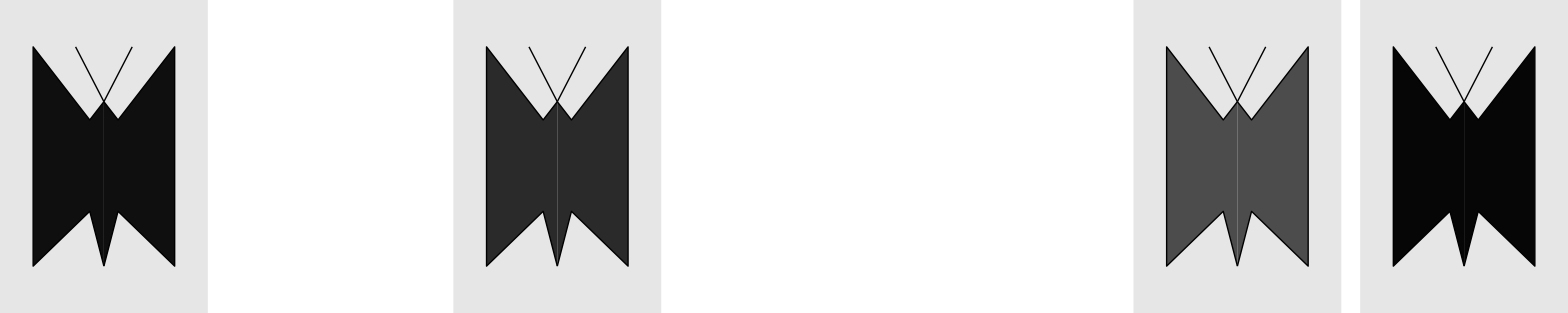

```mathematica
displayButterflyWorld[reductionResults]
```

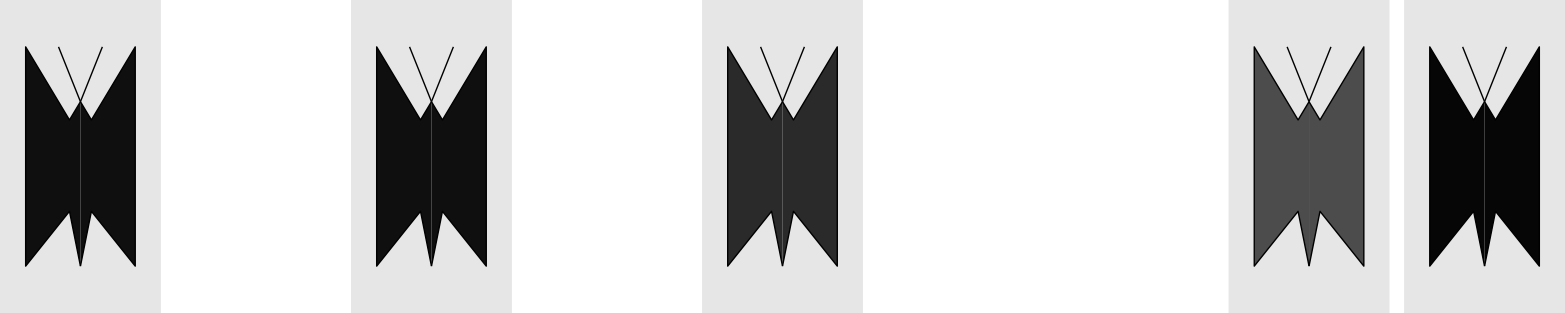

```mathematica
displayButterflyWorld[creationResults]
```

### Main Function ----- Evolution of Butterflies

```mathematica
evolveButterflies[opts___]:=Block[
{initPop,reproIndivs,indivs,butterflyGenerations},

initPop=InitialPopulation/.{opts}/.Options[evolveButterflies];
If[initPop=={},
initPop=createWorld[
WorldWidth/.{opts}/.Options[evolveButterflies],
ButterflyProbability/.{opts}/.Options[evolveButterflies],
opts
]
];

indivs=Count[initPop,{1,_}];

reproIndivs=Round[
Length[initPop] ReductionCreationPortion/.{opts}/.Options[evolveButterflies]
];

butterflyGenerations=NestList[
reductionAndCreation[#1,Min[reproIndivs,indivs],opts]&,
initPop,
Generations/.{opts}/.Options[evolveButterflies]
];

(*(displayButterflyWorld[#1,opts]&)/@butterflyGenerations*)

Return[butterflyGenerations]
];
```

#### Test

Test evolveButterflies function.

```mathematica
butterflies2D=evolveButterflies[
InitialPopulation->{},
WorldWidth->20,
ButterflyProbability->.8,
ReductionCreationPortion->0.5,
Generations->10,
MutationProbability->.2,
MutationRange->0.5,
BackgroundHue->1.,
ColoringFunction->Hue,
DisplayMatrixWidth->5
]
```

{{{1,0.298205},{1,0.0720121},{0,BGColor},{0,BGColor},{0,BGColor},{0,BGColor},{1,0.928844},{1,0.918483},{0,BGColor},{1,0.777383},{0,BGColor},{1,0.295529},{1,0.900022},{1,0.0788303},{1,0.597192},{1,0.983857},{1,0.537048},{0,BGColor},{1,0.87167},{1,0.169574}},{{1,0.983857},{0,BGColor},{0,BGColor},{1,0.983857},{1,0.983857},{1,0.598892},{0,BGColor},{1,0.918483},{1,0.694677},{0,BGColor},{0,BGColor},{1,0.983857},{1,0.900022},{1,0.983857},{0,BGColor},{1,0.983857},{1,0.918483},{1,0.983857},{1,0.983857},{0,BGColor}},{{0,BGColor},{1,0.0687053},{0,BGColor},{1,0.983857},{1,0.983857},{0,BGColor},{1,0.0687053},{0,BGColor},{0,BGColor},{1,0.0687053},{1,0.0687053},{0,BGColor},{1,0.983857},{1,0.0687053},{0,BGColor},{1,0.983857},{1,0.983857},{1,0.983857},{1,0.0687053},{1,0.983857}},{{0,BGColor},{0,BGColor},{0,BGColor},{1,0.983857},{1,0.443539},{1,0.0251693},{0,BGColor},{0,BGColor},{1,0.983857},{1,0.983857},{1,0.0251693},{1,0.983857},{1,0.983857},{0,BGColor},{0,BGColor},{1,0.983857},{1,0.983857},{1,0.983857},{1,0.983857},{1,0.983857}},{{0,BGColor},{1,0.931143},{1,0.234368},{1,0.983857},{0,BGColor},{1,0.983857},{0,BGColor},{0,BGColor},{1,0.234368},{1,0.931143},{0,BGColor},{1,0.931143},{0,BGColor},{1,0.983857},{1,0.863962},{1,0.983857},{1,0.983857},{0,BGColor},{1,0.983857},{1,0.983857}},{{1,0.983857},{1,0.983857},{0,BGColor},{1,0.983857},{0,BGColor},{1,0.983857},{1,0.983857},{1,0.983857},{0,BGColor},{1,0.983857},{0,BGColor},{1,0.983857},{0,BGColor},{1,0.983857},{1,0.983857},{0,BGColor},{0,BGColor},{1,0.983857},{1,0.983857},{1,0.983857}},{{0,BGColor},{0,BGColor},{1,0.983857},{1,0.983857},{1,0.983857},{1,0.983857},{0,BGColor},{1,0.983857},{0,BGColor},{1,0.983857},{1,0.165019},{1,0.865172},{0,BGColor},{0,BGColor},{1,0.983857},{1,0.865172},{0,BGColor},{1,0.232054},{1,0.983857},{1,0.983857}},{{1,0.983857},{0,BGColor},{1,0.496163},{1,0.983857},{1,0.983857},{1,0.983857},{0,BGColor},{0,BGColor},{1,0.983857},{0,BGColor},{1,0.983857},{1,0.983857},{0,BGColor},{0,BGColor},{1,0.983857},{1,0.983857},{1,0.983857},{1,0.983857},{1,0.983857},{0,BGColor}},{{1,0.983857},{1,0.983857},{1,0.983857},{0,BGColor},{1,0.983857},{1,0.983857},{1,0.983857},{0,BGColor},{0,BGColor},{0,BGColor},{1,0.983857},{1,0.983857},{0,BGColor},{1,0.983857},{1,0.983857},{0,BGColor},{1,0.983857},{1,0.983857},{0,BGColor},{1,0.983857}},{{1,0.983857},{0,BGColor},{1,0.983857},{1,0.983857},{1,0.983857},{1,0.983857},{1,0.983857},{1,0.0543573},{0,BGColor},{0,BGColor},{1,0.983857},{1,0.983857},{1,0.889153},{1,0.983857},{0,BGColor},{0,BGColor},{1,0.234795},{1,0.983857},{0,BGColor},{0,BGColor}},{{0,BGColor},{1,0.201485},{0,BGColor},{1,0.983857},{0,BGColor},{1,0.983857},{1,0.983857},{0,BGColor},{1,0.983857},{0,BGColor},{1,0.983857},{0,BGColor},{1,0.201485},{1,0.983857},{0,BGColor},{1,0.983857},{1,0.983857},{1,0.983857},{1,0.933043},{1,0.983857}}}

Now, we display each generation in graphics.

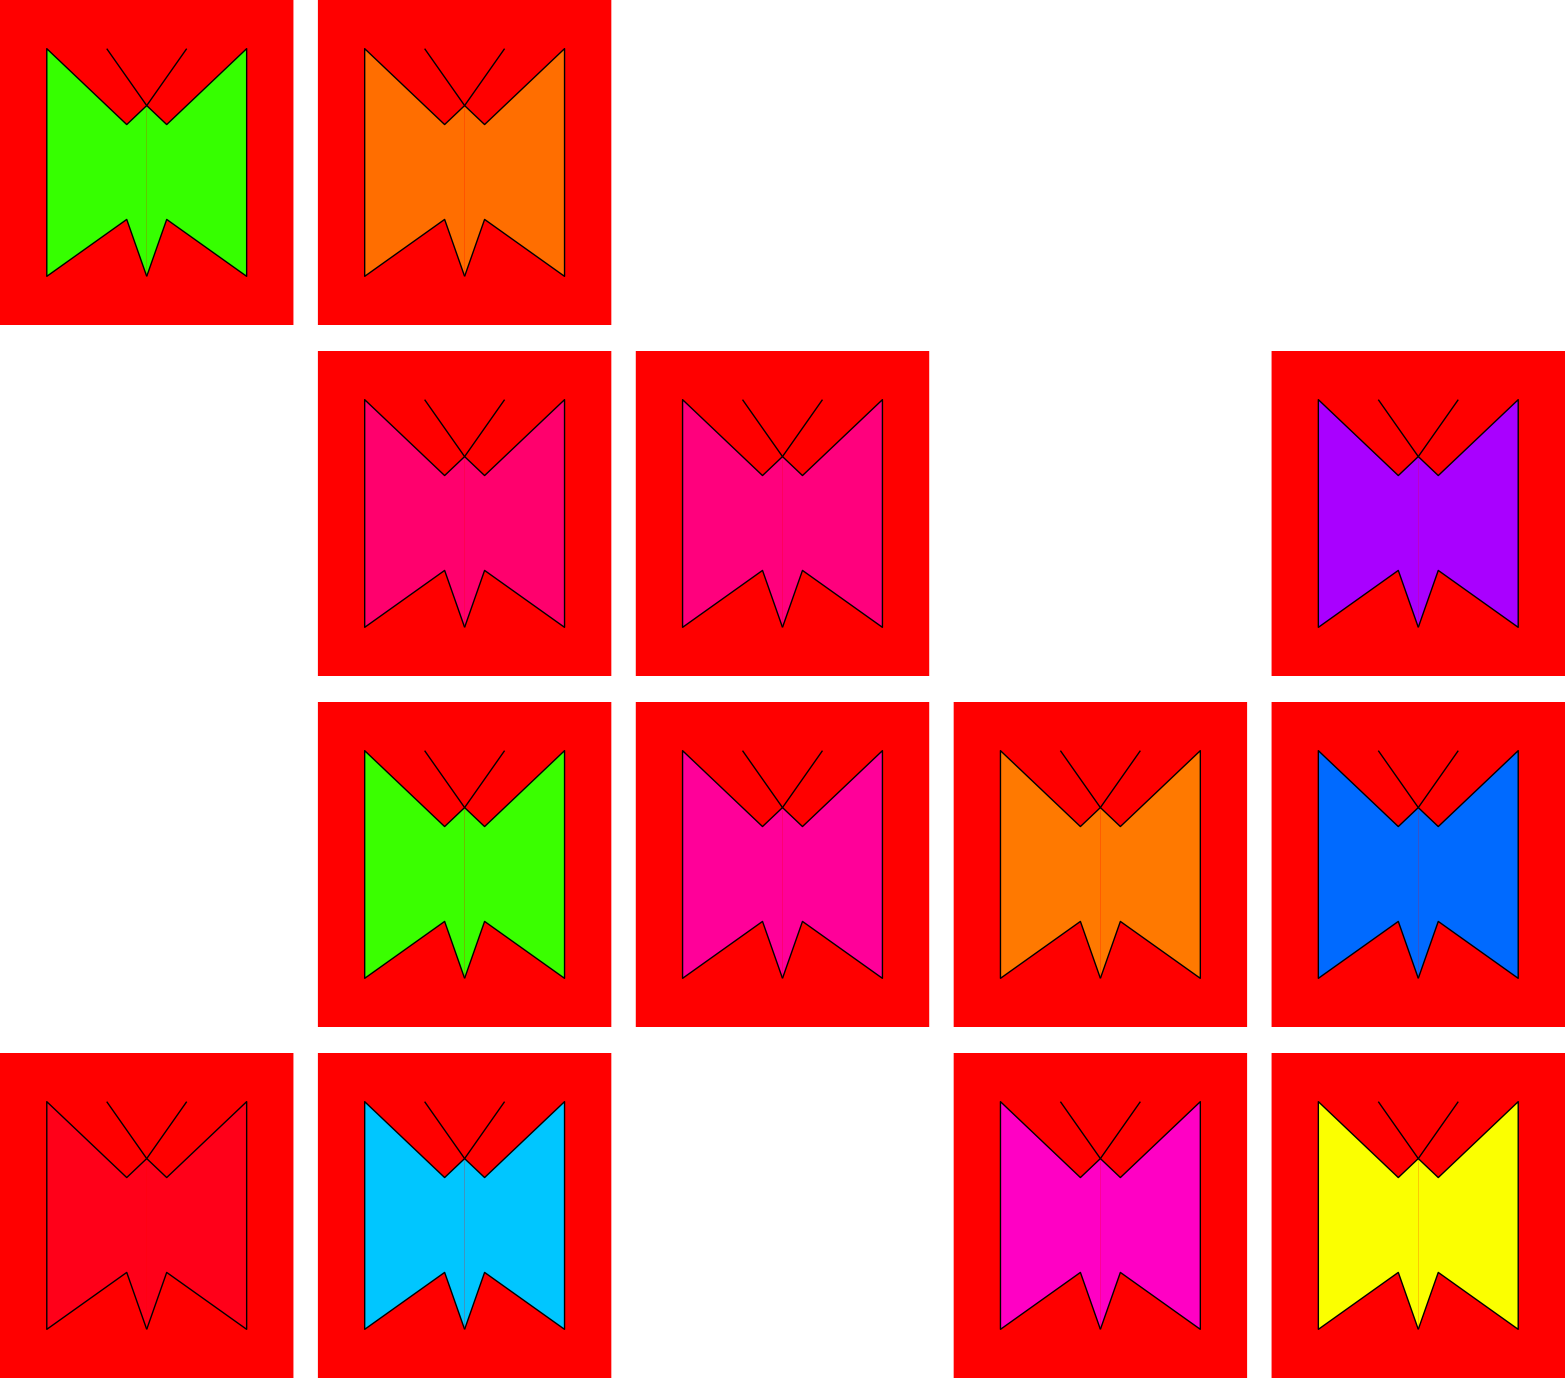
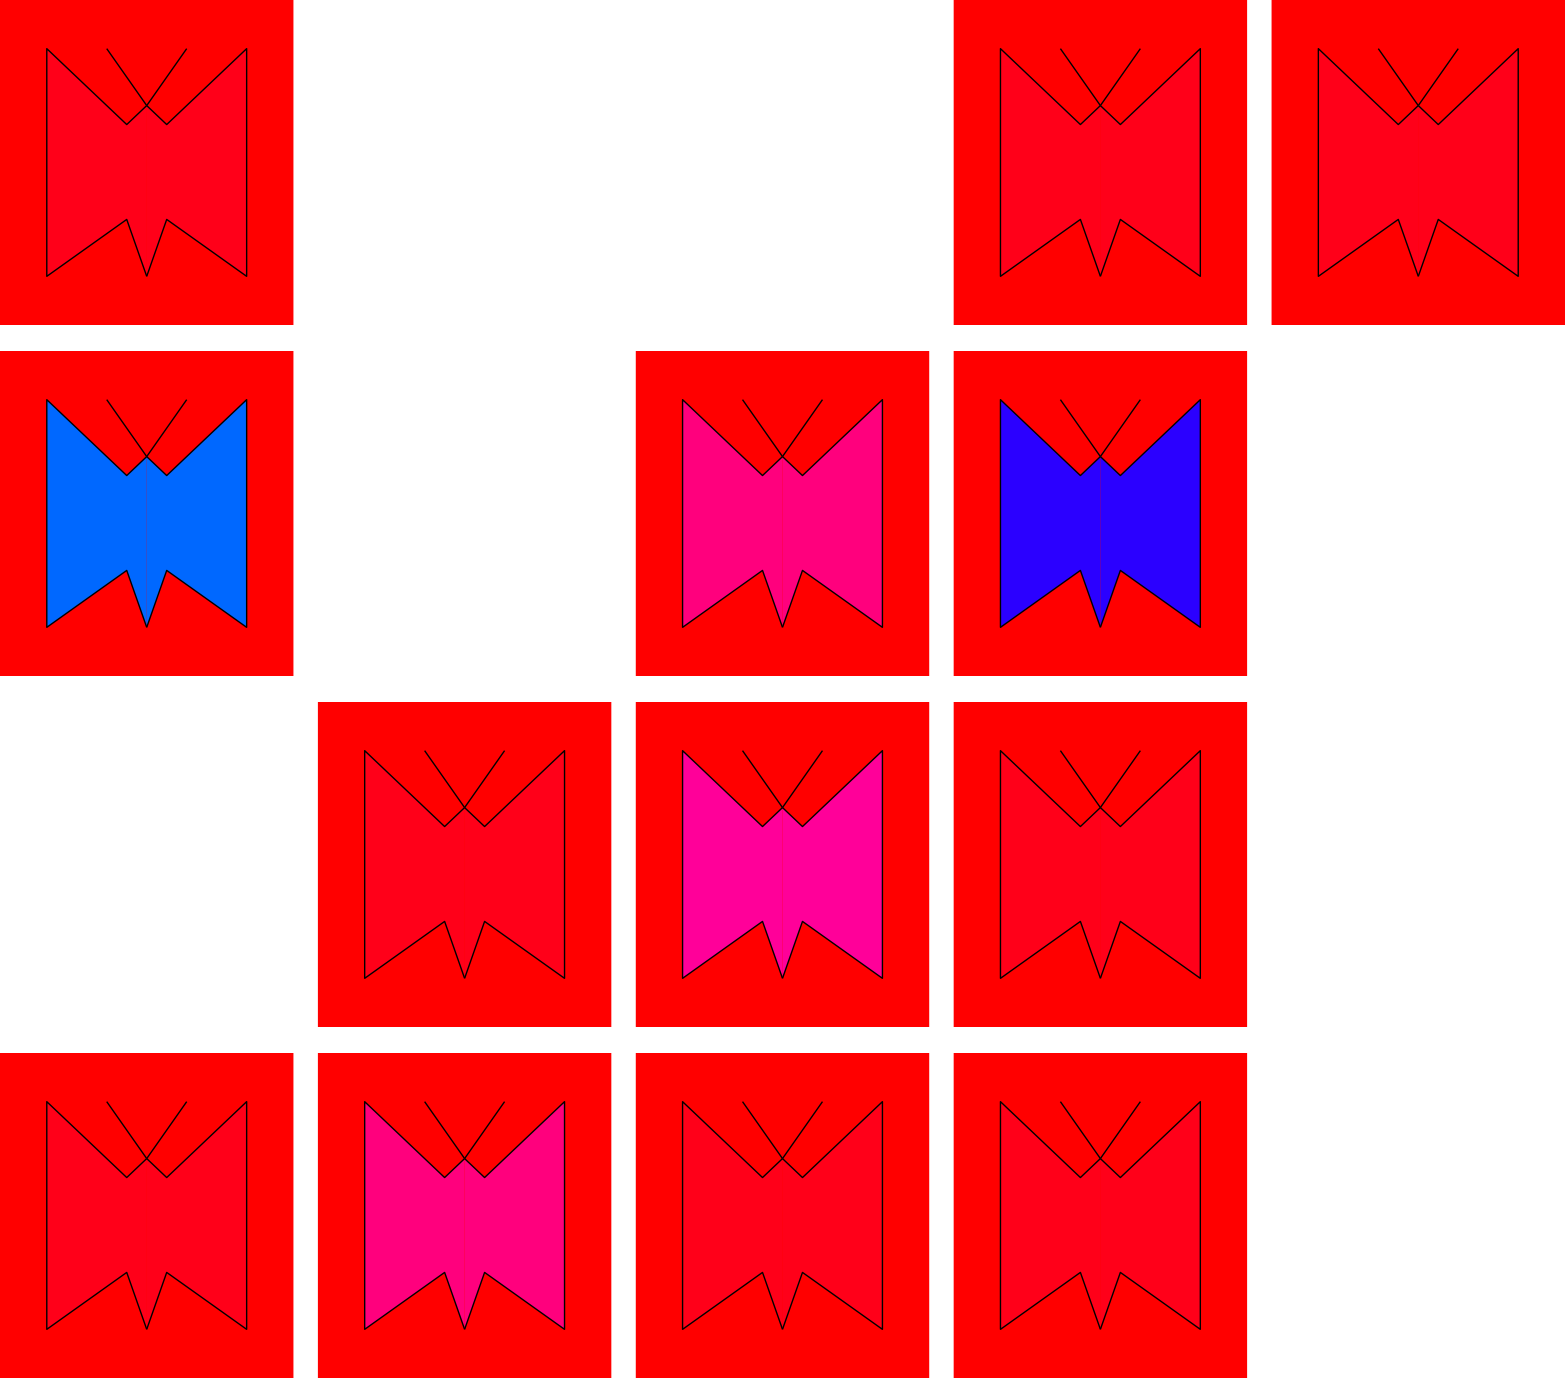
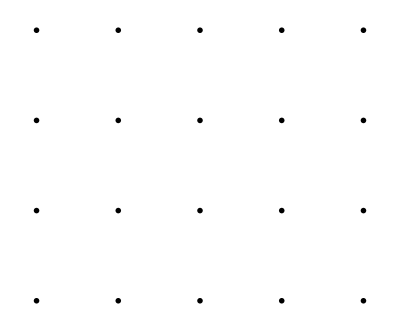
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
displayButterflyWorld[#,BackgroundHue->1.0,ColoringFunction->Hue,DisplayMatrixWidth->5]&/@butterflies2D
```

## Experimentation

### Butterflies on red tree trunk

```mathematica
butterfliesOnRedTree=evolveButterflies[
InitialPopulation->{},
WorldWidth->50,
ButterflyProbability->.8,
ReductionCreationPortion->0.5,
Generations->15,
MutationProbability->.2,MutationRange->0.5,
BackgroundHue->1.,
ColoringFunction->Hue,
DisplayMatrixWidth->10
];
```

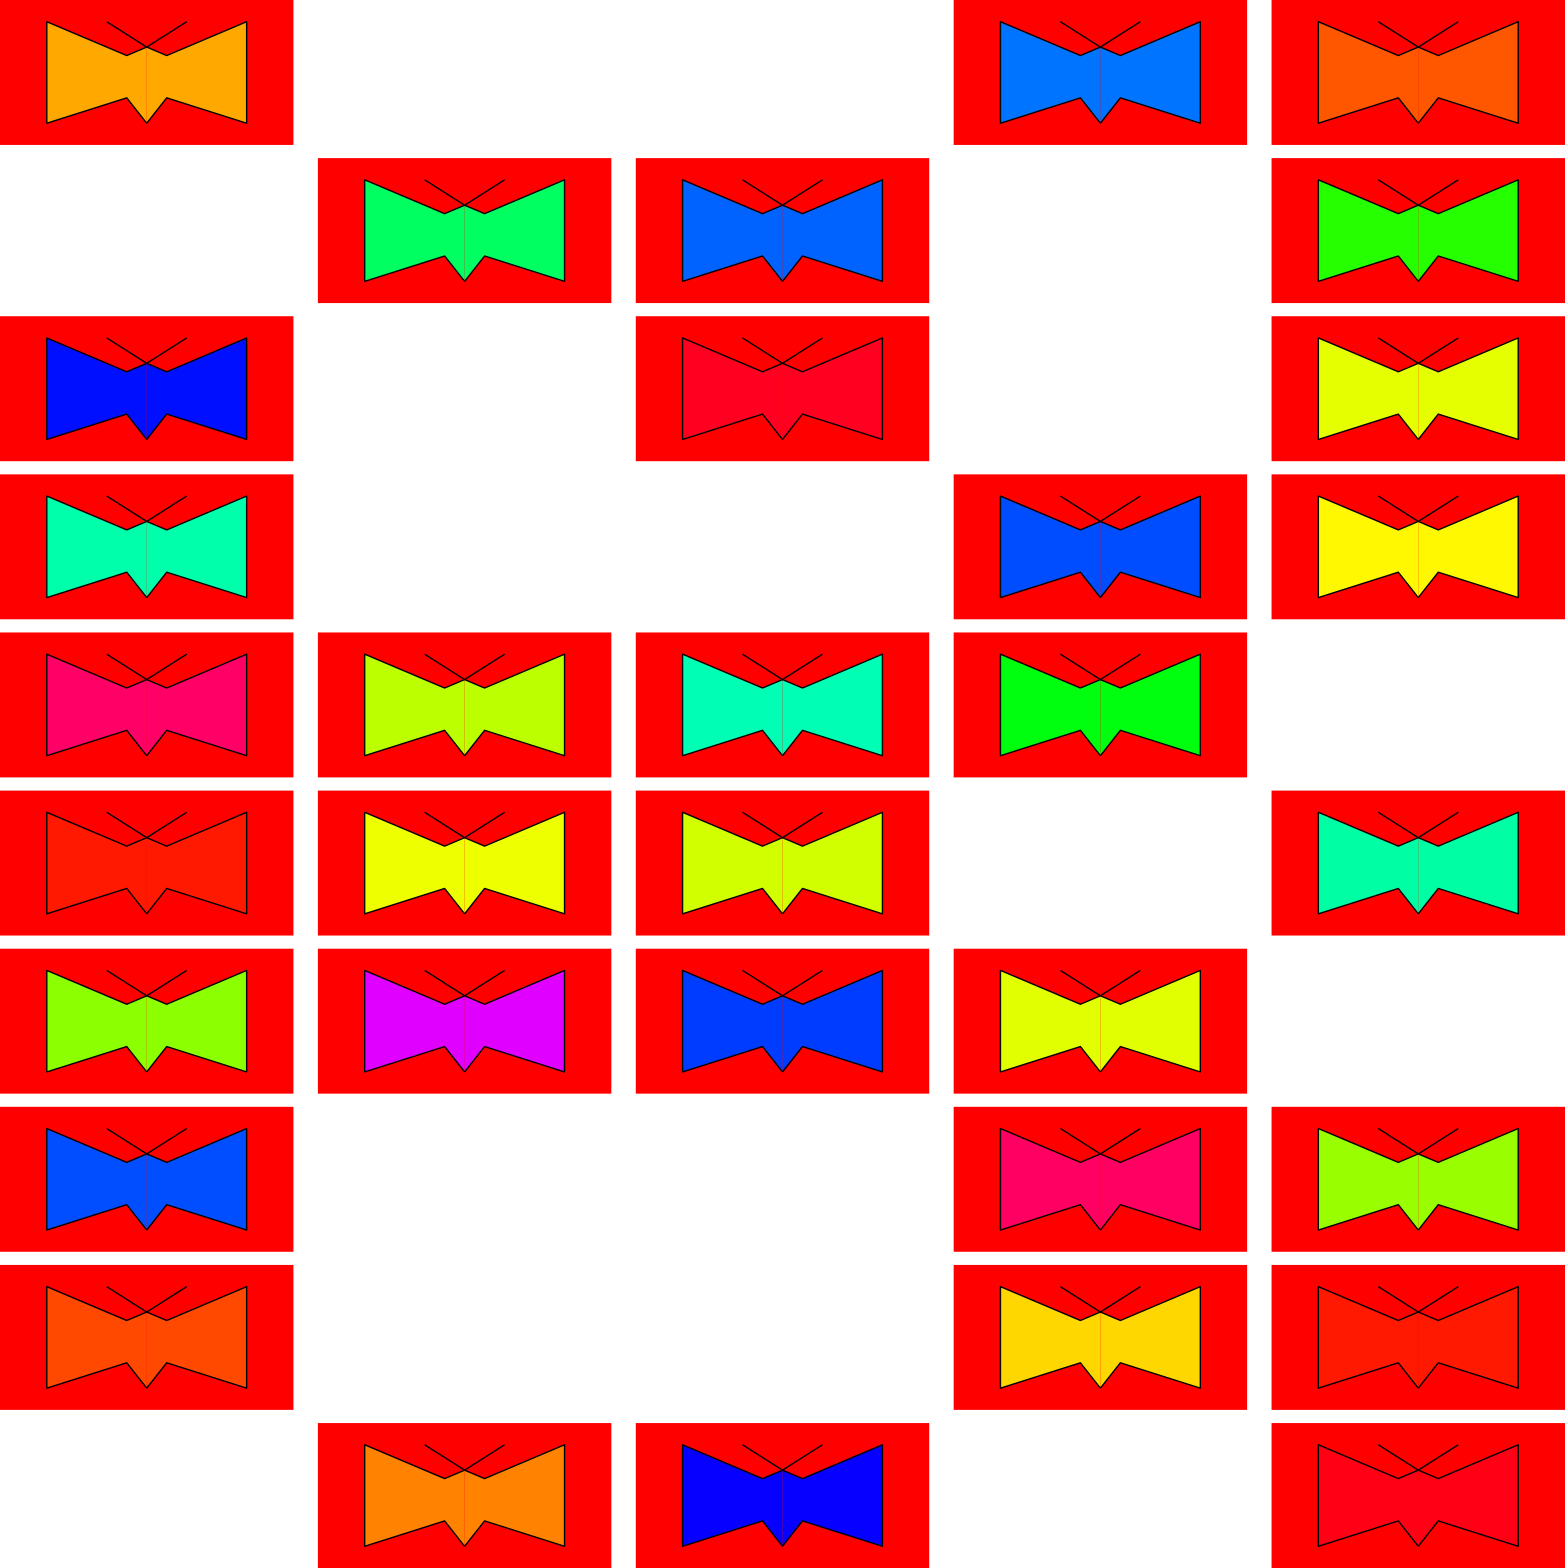
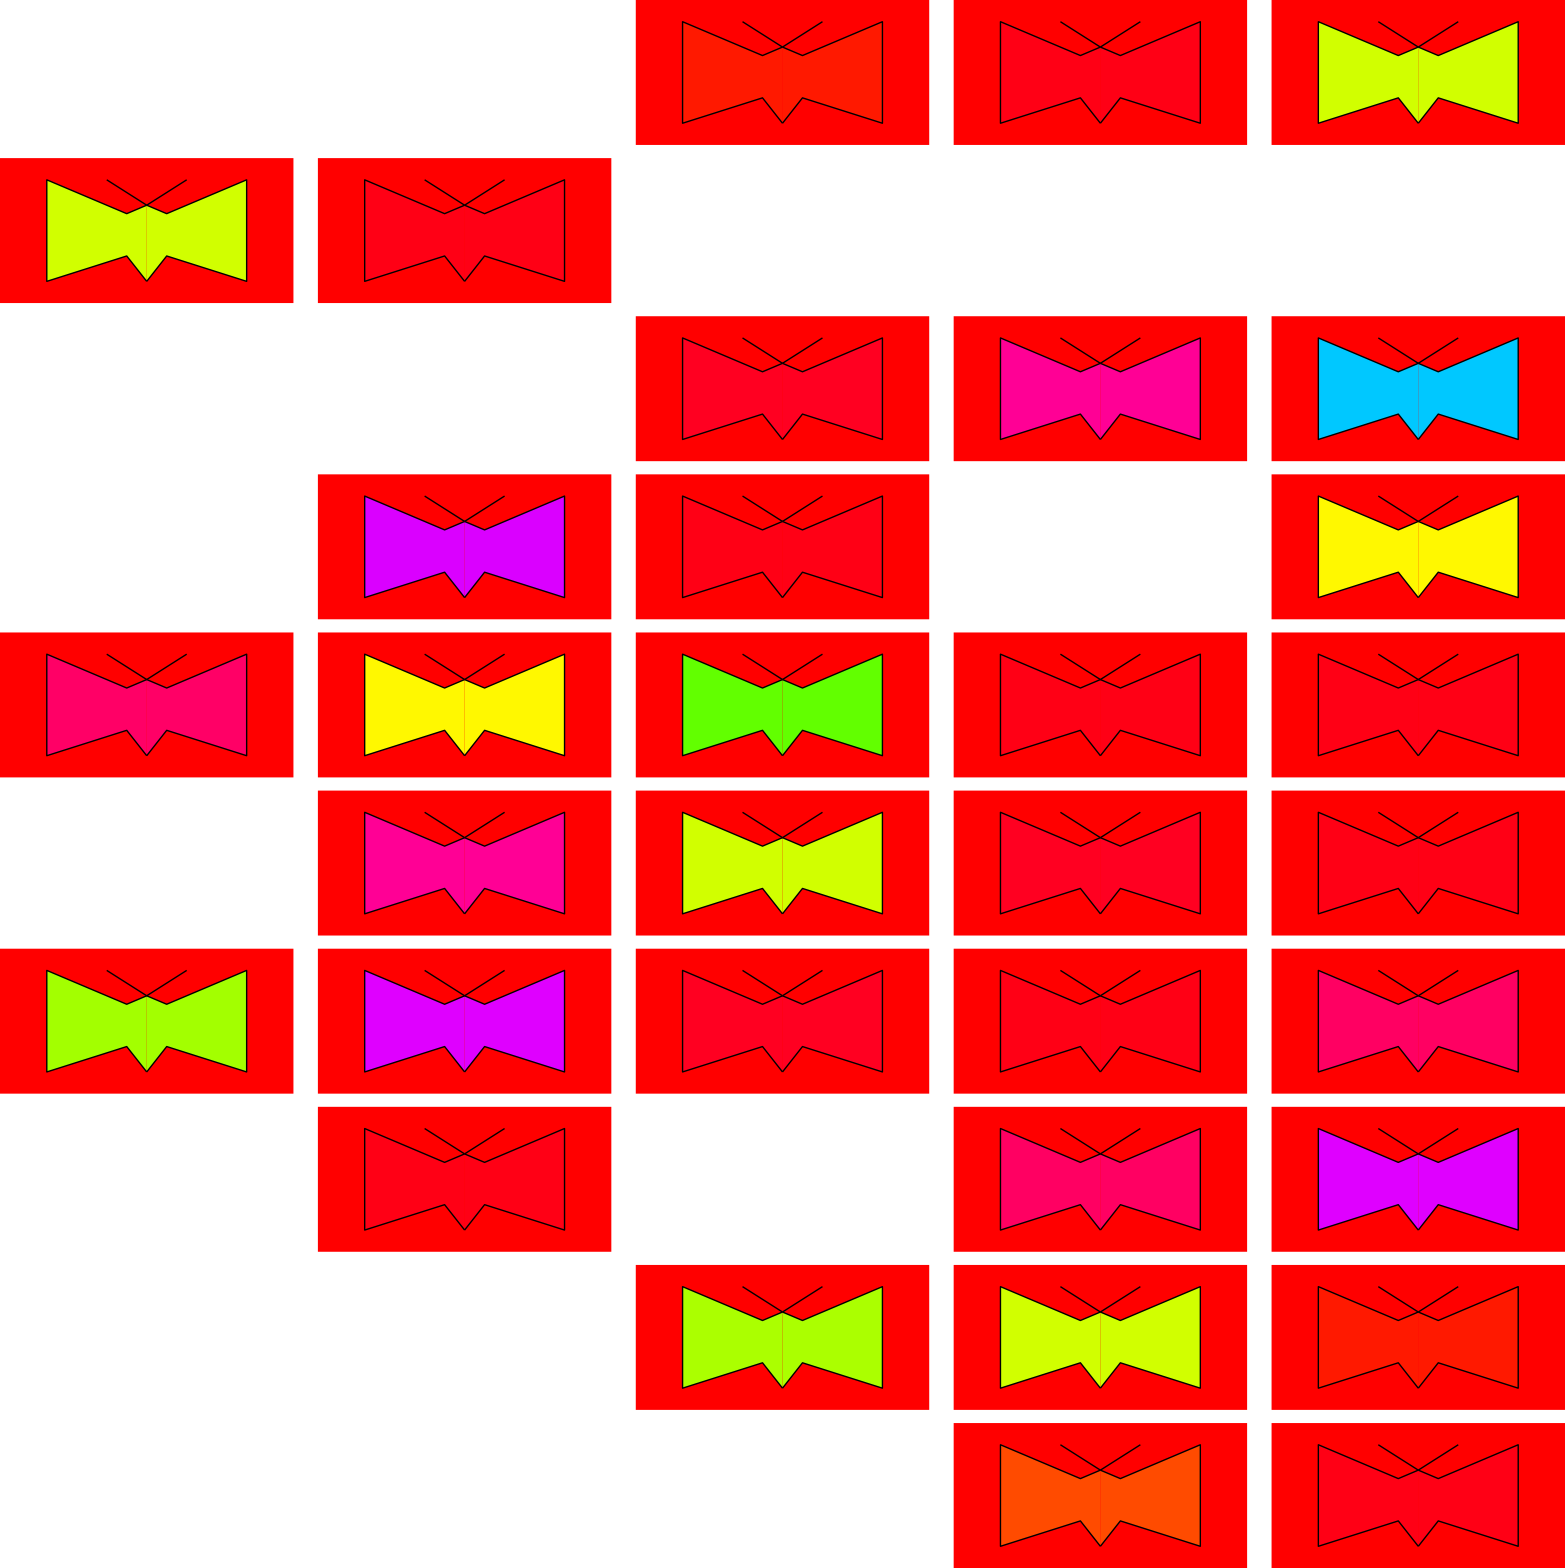
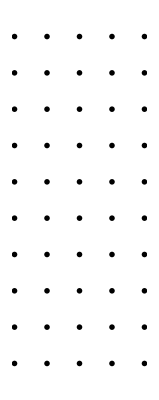
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
displayButterflyWorld[#,BackgroundHue->1.0,ColoringFunction->Hue,DisplayMatrixWidth->5]&/@butterfliesOnRedTree
```

### Butterflies on cyan tree trunk

```mathematica
butterfliesOnCyanTree=evolveButterflies[
InitialPopulation->Last[butterfliesOnRedTree],
WorldWidth->50,
ButterflyProbability->.8,
ReductionCreationPortion->0.5,
Generations->15,
MutationProbability->.2,MutationRange->0.5,
BackgroundHue->.5,
ColoringFunction->Hue,
DisplayMatrixWidth->10
];
```

```mathematica
displayButterflyWorld[#,BackgroundHue->0.5,ColoringFunction->Hue,DisplayMatrixWidth->5]&/@butterfliesOnCyanTree
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Butterflies on light green background

```mathematica
butterfliesOnGreenTree=evolveButterflies[
InitialPopulation->Last[butterfliesOnCyanTree],
WorldWidth->50,
ButterflyProbability->.8,
ReductionCreationPortion->0.5,
Generations->15,
MutationProbability->.2,MutationRange->0.5,
BackgroundHue->.2,
ColoringFunction->Hue,
DisplayMatrixWidth->10
];
```

```mathematica
displayButterflyWorld[#,BackgroundHue->0.2,ColoringFunction->Hue,DisplayMatrixWidth->5]&/@butterfliesOnGreenTree
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Save Data

```mathematica
path="C:\\Users\\zbche_000\\OneDrive\\Documents\\Technical Documents\\Learning Mathematica\\Coder\\Illustrating Evolutionary Computation with Mathematica by Christian Jacob\\";
SetDirectory[path<>"Chapter 01\\Butterflies\\"];
butterflies2D>>"Butterflies2D"
butterfliesOnRedTree>>"ButterfliesOnRedTree"
butterfliesOnCyanTree>>"ButterfliesOnCyanTree"
butterfliesOnGreenTree>>"ButterfliesOnGreenTree"
```